This notebook simulate a self-regulated gene with GA and the three-stage model

# Gillespie One Regulate-gene (auto-activation)

## Parameters

These are the ranges of values for parameters variation. The range of each parameter is divided into smaller ranges (subRanges). In this way the complete range is evaluated in parallel files each one with a subRange of parameters values.

```mathematica
iteraciones=20000; (* Number of algorithm iterations *)
replicas=10; (* Number of times the algorithm is run *)
name=0.5; (* This is the last value of the range for the parameter being evluated *)
kgs=Range[0.01,1,0.01];
γgs=Range[0.02,name,0.02]; (* subRanges: 0.02-0.5, 0.52-1.0, 1.02-1.5, 1.52-2 *)
γms=Range[0.001,0.1(*name*),0.001];(* subRanges: 0.001-0.025, 0.026-0.05, 0.051-0.075, 0.076-0.1 *)
γps=Range[0.001,0.1(*name*),0.001];(* subRanges: 0.001-0.025, 0.026-0.05, 0.051-0.075, 0.076-0.1 *)
parametro="γg"; (* With the name of the second parameter is named the output file *)
```

These are the default values of parameters

```mathematica
Clear[kg,γg,km,γm,kp,γp,τ];
kg=0.01158;(*α: binding probability*)
γg=2.082;(*α_: unbinding probability*)
km=0.696(*syntesis mRNA *);
γm=0.02082(*degradation mRNA*);
kp=1.386(*syntesis proteins*);
γp=0.02082(*degradation proteins*);
h=3.0;  (* Hill's constant *);
```

## Functions

These are the reactions (changesByRXN) and propensity functions (pF) of the GA for the specific regulation system: A: Activator -> B : Activated gene

```mathematica
changesByRXN=Function/@<|1->{#1,#2,#3-1,#4+1},2->{#1,#2,#3+1,#4-1},3->{#1+1,#2,#3,#4},4->{#1-1,#2,#3,#4},5->{#1,#2+1,#3,#4},6->{#1,#2-1,#3,#4}|>;(* Each hash represents a specie: mRNA,protein,da0,da1. Reactions: 1-activation, 2-deactivation, 3-5 synthesis, 4-6 degradation *)pF=Compile[{{kg,_Real},{γg,_Real},{km,_Real},{γm,_Real},{kp,_Real},{γp,_Real},{h,_Real},{a,_Integer},{p,_Integer},{da0,_Integer},{da1,_Integer}},{da0*kg*(a ^h/((γg/kg)+a ^h)),da1*γg,da1*km+0.01(*Esto para mantener una expresión basal como en el de Langevin (que no tiene ceros)y que el kon no se haga cero*),a*γm,kp*a,γp*p},RuntimeAttributes->{Listable},Parallelization->True];
```

```mathematica
ff[dato_]:=N[Variance[dato]/Mean[dato]];(* Fano Factor for noise measure *)
expressionNoise[data_]:=N[Variance[data]/Mean[data]^2](* Squared Coefficient of Variation for noise measure *)
```

## Simulation

```mathematica
mRNAffcv2List={};
proteinffcv2List={};
Table[
listEstimatemRNA={};
listEstimateprotein={};
listDataT={};
timesT={};
Table[
listData={};times={};t=0;AppendTo[times,t];abundancia={1,1,1,0}(*mRNA,protein,da0,da1*);AppendTo[listData,abundancia];
Do[
τis=Map[If[#>0,RandomVariate[ExponentialDistribution[#]],∞]&,pF[kg,γg,km,γm,kp,γp,h,Sequence@@abundancia]];reactionAndτμ={FirstPosition[#,Min[#]],Min[#]}&[τis];abundancia=Through[{reactionAndτμ[[1]]/.changesByRXN}[[1,1]]@@abundancia][[1]];AppendTo[listData,abundancia];t=t+reactionAndτμ[[2]];AppendTo[times,t],iteraciones];
{mRNAffcv2It,proteinffcv2It}=Table[{ff1[Flatten@i],expressionNoise[Flatten@i]},{i,{listData[[10000;;All,1]],
listData[[10000;;All,2]]}}];
AppendTo[listEstimatemRNA,mRNAffcv2It];
AppendTo[listEstimateprotein,proteinffcv2It];
AppendTo[listDataT,listData];
AppendTo[timesT,times],replicas];
AppendTo[mRNAffcv2List,Mean[listEstimatemRNA]];
AppendTo[proteinffcv2List,Mean[listEstimateprotein]],{kg,{0.8}},{γg,{1.5}}];
```

```mathematica
Export["controlRGA_"<>parametro<>ToString[name],{mRNAffcv2List,proteinffcv2List},"CSV"]
```

controlRGA_γg0.5

## Graphs

```mathematica
{mRNAffcv2List,proteinffcv2List}
```

{{{0.708818,0.0561729}},{{21.5404,0.0262556}}}

```mathematica
label="FF: "<>ToString[mRNAffcv2List[[1,1]]]<>" | "<>ToString[proteinffcv2List[[1,1]]]<>" kon: 0.8, koff: 1.5, ksm: 0.696, kdm: 0.02, \nksp: 1.386, kdp:0.0282, GA OneG R, primeras 20mil";datesList=Table[{timesT[[i,j]],listDataT[[i,j,1]]},{i,Length[listDataT]},{j,Length[listDataT[[1]]]}];
```

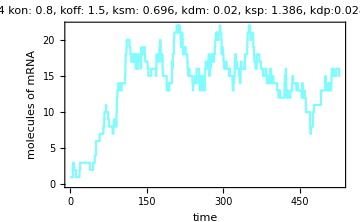

```mathematica
ListLinePlot[datesList[[1]],Frame-> True,PlotStyle->
RGBColor[0.5,0.99,1],ImageSize->Medium,FrameLabel->{"time","molecules of mRNA"},PlotLabel->label]
```

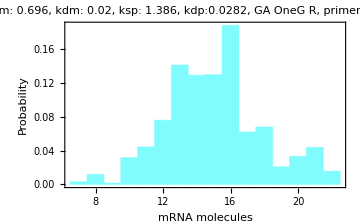

```mathematica
distribucion=Flatten@listDataT[[1,10000;;All,1]];
Histogram[distribucion,"Scott","Probability",Frame->True,FrameLabel->{"mRNA molecules","Probability"},PlotLabel->label<>" FF: "<>ToString[ff1[distribucion]]<>", CV^2: "<>ToString[expressionNoise[distribucion]]<>", Mean: "<>ToString[Mean[distribucion]//N],ChartStyle->RGBColor[0.5,0.99,1],ImageSize->Medium]
```

```mathematica
datesListP=Table[{timesT[[i,j]],listDataT[[i,j,2]]},{i,Length[listDataT]},{j,Length[listDataT[[1]]]}];
```

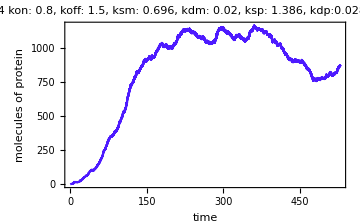

```mathematica
ListLinePlot[datesListP[[1]],Frame-> True,PlotStyle->
RGBColor[0.3,.1,1],ImageSize->Medium,FrameLabel->{"time","molecules of protein"},PlotLabel->label]
```

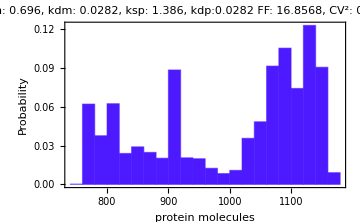

```mathematica
distribucion=listDataT[[1,10000;;All,2]];
Histogram[distribucion,"Scott","Probability",Frame->True,FrameLabel->{"protein molecules","Probability"},PlotLabel->" kon:1, koff:2, ksm: 0.696, kdm: 0.0282, \nksp: 1.386, kdp:0.0282"<>" FF: "<>ToString[ff1[distribucion]]<>", CV^2: "<>ToString[expressionNoise[distribucion]]<>", Mean: "<>ToString[Mean[distribucion]//N],ChartStyle->RGBColor[0.3,.1,1],ImageSize->Medium]
```